```mathematica
eps=RQATimeSeriesEpochs[ts,100,20];
```

```mathematica
taus=Map[RQAEstimateLag,eps]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{22.268,30.6196,35.6073,35.0889,36.1694,32.624,37.1057}

```mathematica
Mean[%]
```

32.7833

```mathematica
embeds=Map[RQAEmbed[#,3,30.0]&,eps]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

```mathematica
maps=RQADistanceMap/@embeds;
```

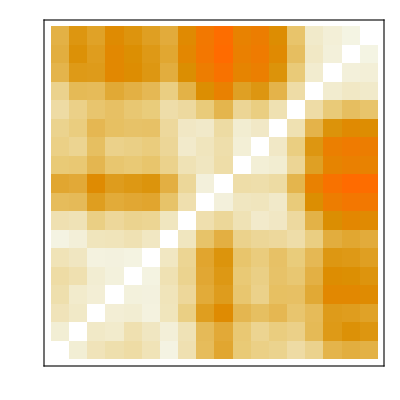
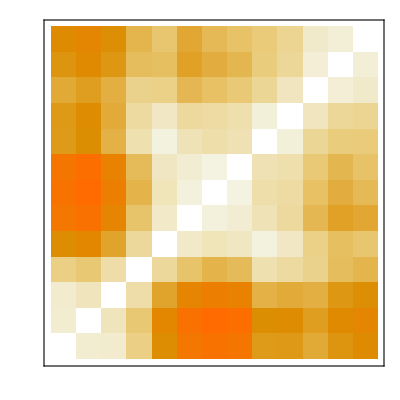
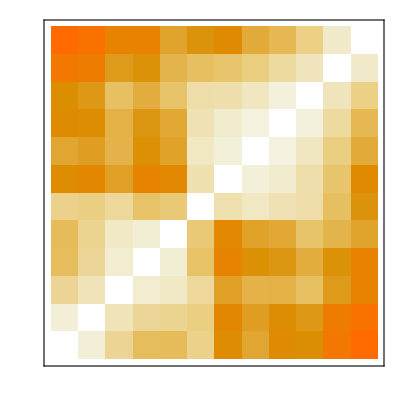
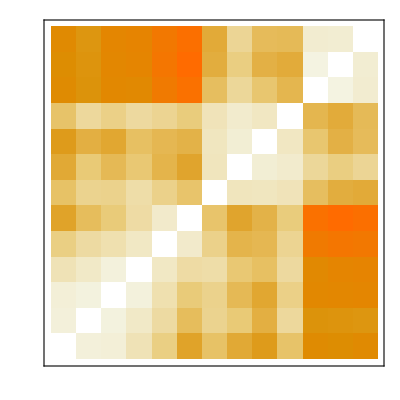
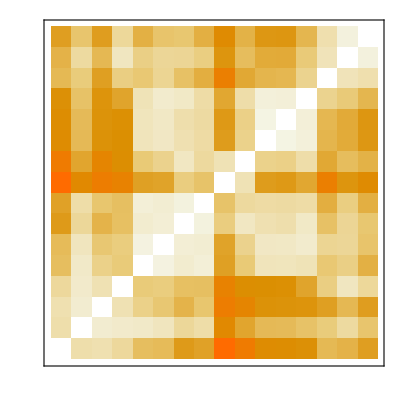
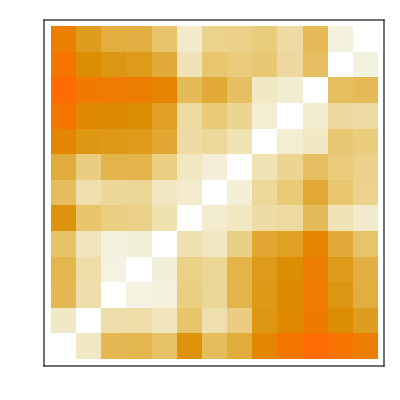
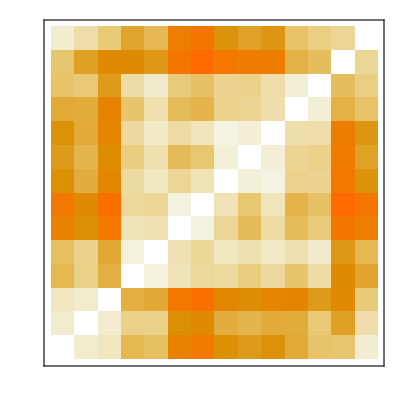

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None]&/@maps
```